# Data Science and Machine Learning II

## Assignment 3: MovieLens genre associations - using associative rules learning to analyze genres co-occurrences

In this assignment, we will explore the co-occurrences of the genres assigned to a movie (e.g., the movie is both Action and Comedy). 

We will use the publicly-available MovieLens dataset.
Source: F. Maxwell Harper and Joseph A. Konstan. 2015. The MovieLens Datasets: History and Context. ACM Transactions on Interactive Intelligent Systems (TiiS) 5, 4: 19:1–19:19. https://doi.org/10.1145/2827872

We will apply the Apriori Algorithm, developed by Anton Antonov, and available in the GitHub repository MathematicaForPrediction. This repository contains many implementations of  statistical and Machine Learning algorithms in Wolfram that can be used for data analysis, forecast, prediction, and recommendation systems.

This assignment was inspired by the post Movie genre associations, also by Anton Antonov. Feel free to check this post, and the documentation available in the GitHub repository MathematicaForPrediction. It might help you complete the assignment ;)  

Once you are done you have to submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1224213
There is no quiz, so your grade will depend only on your notebook.
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

## Discover your dataset

Question 1: 
- Import as a dataset the CSV file "movies.csv", which you can find in GitHub: "https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_3/movies.csv"
- Discover the dataset by displaying a random sample and the dimensions of your dataset    
[1 point]

```mathematica
dataset = Import["https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_3/movies.csv", "Dataset", "HeaderLines" -> 1];
RandomSample[dataset,7]
```

```mathematica
Dimensions[dataset]
```

{9742,3}

### Cleaning/Formatting

Question 2: 
We will explore the column "genres" of movies. 
- Create a list containing the genres.
- As you may have noticed, the genres are separated by the "|" symbol. Change the structure of your previous list, creating a list of list. Your output should be something like:
{{Adventure, Animation, Children, Comedy, Fantasy}, {Adventure, Children, Fantasy}, ...} 
[1 point]

Hint: Each item in our original list is a string. You can use StringSplit to split a string based on a given pattern/symbol. Try with one item of our original list, and then apply the same operations to all the elements of your original list.

```mathematica
genres = Normal @ dataset[All,"genres"];
genres = Map[StringSplit[#,  "|" ] &,genres,2]
```

### Number of genres per movies

Question 3: 
- Create a list containing the number of genres per movie, i.e., your output should look like: {5,3,2,...}
- Find the minimum, maximum, average, and median number of genres.
[1 point]

```mathematica
nbGenres = Map[Length,genres,2]
```

```mathematica
Dataset[<|"Min number of genres" -> Min[nbGenres],
"Max number of genres" -> Max[nbGenres], 
"Average number of genres" -> N @Mean[nbGenres],
"Median number of genres" -> Median[nbGenres] |>]
```

Question 4: 
Create a histogram of the number of genres per movie. 
 [1 point]

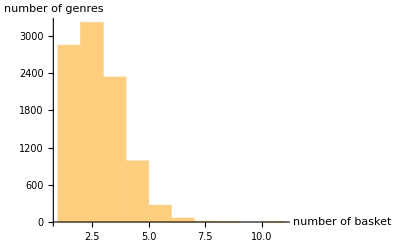

```mathematica
Histogram[nbGenres, AxesLabel ->{"number of basket","number of genres"}]
```

### Number of appearances of each genre

Question 5: 
- Create a list containing all the movie genres (unique values).
- Count the number of appearance of each genre, i.e., the number of movies that are identified with each genre, and store the result in a list.
- Create an association between a given genre (keys) and the associated number of appearance (values), sorted by the number of number of appearances (from most appearances to least). 
- Display your result in a dataset
 [1 point]

```mathematica
genresList = DeleteDuplicates[Flatten @ genres]
```

{Adventure,Animation,Children,Comedy,Fantasy,Romance,Drama,Action,Crime,Thriller,Horror,Mystery,Sci-Fi,War,Musical,Documentary,IMAX,Western,Film-Noir,(no genres listed)}

```mathematica
countGenres = Map[Count[Flatten @ genres,#]&,genresList]
```

{1263,611,664,3756,779,1596,4361,1828,1199,1894,978,573,980,382,334,440,158,167,87,34}

```mathematica
assoGenresCount = ReverseSort @ AssociationThread[genresList ->countGenres]
```

<|Drama→4361,Comedy→3756,Thriller→1894,Action→1828,Romance→1596,Adventure→1263,Crime→1199,Sci-Fi→980,Horror→978,Fantasy→779,Children→664,Animation→611,Mystery→573,Documentary→440,War→382,Musical→334,Western→167,IMAX→158,Film-Noir→87,(no genres listed)→34|>

```mathematica
Dataset @ assoGenresCount
```

## Apriori algorithm

Question 6:   
- Use Get to read the "AprioriAlgorithm.m" file available in the GitHub folder at this address: "https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_3/AprioriAlgorithm.m"
- Display Information about the function AprioriApplication, which contains the implementation in Wolfram of the Apriori Algorithm. We will use this function in the following
 [1 point]

```mathematica
Get["https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_3/AprioriAlgorithm.m"]
```

```mathematica
?AprioriApplication
```

Question 7:   
The function AprioriApplication takes as first argument a basket of items (e.g., a list of lists), as second argument the minimum frequency of baskets, and as optional argument the maximum number of items "MaxNumberOfItems". It returns a list of 3 elements:
   1. a list of list containing, for each number of items, the frequent baskets. Note that initial items (here, movie genres) are converted to integers.
   2. a mapping between our initial items and integer IDs used in the algorithm.
   3. a mapping between the integer IDs and the initial items .

Call the AprioriApplication, using as argument the output of question 2 (list of lists containing the genres per movie), 0.0025 (2.5%) as minimum frequency, and 4 maximum number of items . Store the results in a list: {aprioriRes, itemToIDRules, idToItemRules} 
 [1 point]

```mathematica
{aprioriRes, itemToIDRules, idToItemRules} =AprioriApplication[genres, 0.0025, "MaxNumberOfItems"-> 4];
```

Question 8:   
Find the number of frequent baskets for each number of items per basket.   
[1 point]

Hint: The frequent baskets are stored in your variable "aprioriRes".

```mathematica
Dataset @ AssociationThread[{1,2,3,4} ->Length /@ aprioriRes]
```

Question 9:   
We will now focus on the frequent baskets containing 2 items.

- From aprioriRes, extract the list of frequent baskets containing 2 items
- Convert the integers to the associated movie genres, using idToItemRules, and store the result in a list (of lists)
 [1 point]

Hint: You can use the function ReplaceAll

```mathematica
frequentBasket2Items = aprioriRes[[2,All]] /. idToItemRules
```

{{Action,Adventure},{Action,Animation},{Action,Children},{Action,Comedy},{Action,Crime},{Action,Drama},{Action,Fantasy},{Action,Horror},{Action,IMAX},{Action,Mystery},{Action,Romance},{Action,Sci-Fi},{Action,Thriller},{Action,War},{Action,Western},{Adventure,Animation},{Adventure,Children},{Adventure,Comedy},{Adventure,Crime},{Adventure,Drama},{Adventure,Fantasy},{Adventure,Horror},{Adventure,IMAX},{Adventure,Musical},{Adventure,Mystery},{Adventure,Romance},{Adventure,Sci-Fi},{Adventure,Thriller},{Adventure,War},{Adventure,Western},{Animation,Children},{Animation,Comedy},{Animation,Drama},{Animation,Fantasy},{Animation,IMAX},{Animation,Musical},{Animation,Romance},{Animation,Sci-Fi},{Children,Comedy},{Children,Drama},{Children,Fantasy},{Children,IMAX},{Children,Musical},{Children,Romance},{Children,Sci-Fi},{Comedy,Crime},{Comedy,Documentary},{Comedy,Drama},{Comedy,Fantasy},{Comedy,Horror},{Comedy,IMAX},{Comedy,Musical},{Comedy,Mystery},{Comedy,Romance},{Comedy,Sci-Fi},{Comedy,Thriller},{Comedy,War},{Comedy,Western},{Crime,Drama},{Crime,Film-Noir},{Crime,Horror},{Crime,Mystery},{Crime,Romance},{Crime,Sci-Fi},{Crime,Thriller},{Drama,Fantasy},{Drama,Film-Noir},{Drama,Horror},{Drama,IMAX},{Drama,Musical},{Drama,Mystery},{Drama,Romance},{Drama,Sci-Fi},{Drama,Thriller},{Drama,War},{Drama,Western},{Fantasy,Horror},{Fantasy,IMAX},{Fantasy,Musical},{Fantasy,Mystery},{Fantasy,Romance},{Fantasy,Sci-Fi},{Fantasy,Thriller},{Film-Noir,Thriller},{Horror,Mystery},{Horror,Sci-Fi},{Horror,Thriller},{IMAX,Sci-Fi},{IMAX,Thriller},{Musical,Romance},{Mystery,Romance},{Mystery,Sci-Fi},{Mystery,Thriller},{Romance,Sci-Fi},{Romance,Thriller},{Romance,War},{Sci-Fi,Thriller},{Thriller,War}}

Question 10:   
Count the number of appearances of each basket of  2 items (list created in question 9) in our original list of genres per movie (question 2), and store the result in a list
 [1 point]

```mathematica
freqGenreBasket = Map[Count[genres,#]&, frequentBasket2Items]
```

{32,6,2,92,32,62,2,9,1,1,2,38,60,13,7,2,23,36,0,41,13,0,0,0,0,6,15,2,1,6,28,30,7,6,0,2,2,8,74,18,6,0,2,0,2,101,31,435,33,69,0,34,7,363,34,17,16,14,134,10,2,7,1,1,45,24,7,26,0,44,38,349,30,168,114,16,7,0,0,0,3,2,0,3,14,53,135,0,0,4,0,2,31,4,6,2,23,0}

Question 11:   
- Create an association between the frequent baskets containing 2 items (question 9) and their number of appearances (question 10). 
- Sort your association by the number of appearances of each basket, from most to least appearances. 
- Display your result in a dataset
- What are the 3 most common basket of genres?
[1 point]

```mathematica
assoBasketNumber =ReverseSort @ AssociationThread[frequentBasket2Items ->freqGenreBasket]
```

<|{Comedy,Drama}→435,{Comedy,Romance}→363,{Drama,Romance}→349,{Drama,Thriller}→168,{Horror,Thriller}→135,{Crime,Drama}→134,{Drama,War}→114,{Comedy,Crime}→101,{Action,Comedy}→92,{Children,Comedy}→74,{Comedy,Horror}→69,{Action,Drama}→62,{Action,Thriller}→60,{Horror,Sci-Fi}→53,{Crime,Thriller}→45,{Drama,Musical}→44,{Adventure,Drama}→41,{Drama,Mystery}→38,{Action,Sci-Fi}→38,{Adventure,Comedy}→36,{Comedy,Sci-Fi}→34,{Comedy,Musical}→34,{Comedy,Fantasy}→33,{Action,Crime}→32,{Action,Adventure}→32,{Mystery,Thriller}→31,{Comedy,Documentary}→31,{Drama,Sci-Fi}→30,{Animation,Comedy}→30,{Animation,Children}→28,{Drama,Horror}→26,{Drama,Fantasy}→24,{Sci-Fi,Thriller}→23,{Adventure,Children}→23,{Children,Drama}→18,{Comedy,Thriller}→17,{Drama,Western}→16,{Comedy,War}→16,{Adventure,Sci-Fi}→15,{Horror,Mystery}→14,{Comedy,Western}→14,{Adventure,Fantasy}→13,{Action,War}→13,{Crime,Film-Noir}→10,{Action,Horror}→9,{Animation,Sci-Fi}→8,{Fantasy,Horror}→7,{Drama,Film-Noir}→7,{Crime,Mystery}→7,{Comedy,Mystery}→7,{Animation,Drama}→7,{Action,Western}→7,{Romance,Thriller}→6,{Children,Fantasy}→6,{Animation,Fantasy}→6,{Adventure,Western}→6,{Adventure,Romance}→6,{Action,Animation}→6,{Romance,Sci-Fi}→4,{Musical,Romance}→4,{Film-Noir,Thriller}→3,{Fantasy,Romance}→3,{Romance,War}→2,{Mystery,Sci-Fi}→2,{Fantasy,Sci-Fi}→2,{Crime,Horror}→2,{Children,Sci-Fi}→2,{Children,Musical}→2,{Animation,Romance}→2,{Animation,Musical}→2,{Adventure,Thriller}→2,{Adventure,Animation}→2,{Action,Romance}→2,{Action,Fantasy}→2,{Action,Children}→2,{Crime,Sci-Fi}→1,{Crime,Romance}→1,{Adventure,War}→1,{Action,Mystery}→1,{Action,IMAX}→1,{Thriller,War}→0,{Mystery,Romance}→0,{IMAX,Thriller}→0,{IMAX,Sci-Fi}→0,{Fantasy,Thriller}→0,{Fantasy,Mystery}→0,{Fantasy,Musical}→0,{Fantasy,IMAX}→0,{Drama,IMAX}→0,{Comedy,IMAX}→0,{Children,Romance}→0,{Children,IMAX}→0,{Animation,IMAX}→0,{Adventure,Mystery}→0,{Adventure,Musical}→0,{Adventure,IMAX}→0,{Adventure,Horror}→0,{Adventure,Crime}→0|>

```mathematica
datasetFrequentBasket2Items =Transpose @ Dataset[<|"Item 1" ->Transpose[Keys[assoBasketNumber]][[1]],"Item 2" ->Transpose[Keys[assoBasketNumber]][[2]],"Number of baskets" ->Values[assoBasketNumber]|>]
```